Distribution.txt

ErrorList.txt

-Graphics3D-

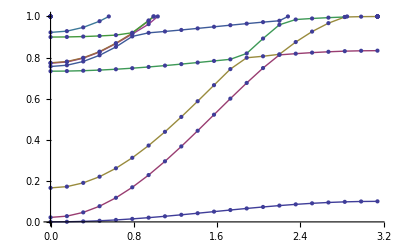

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Get["Methods.m",Path->FileNameJoin[{Directory[],"Packages"}]]

ϵ1=10.;
ϵ2=5.;
H=12.;(*Height of first layer in angstroms*)
a= 3.904;(*unit cell size in angstroms*)
t1=.25;(*hopping parameters in eV*)
t2=.025;
MM=12;
NN=6;
β=.95;(*percent of the old distribution to keep when calculating the new distribution*)
numPartitions=20;
numStates=20;

SetParameters[ϵ1,ϵ2,H, a,  t1,t2, MM, NN, β, numPartitions, numStates];
Initialize[];
firstGuess=Flatten[Table[
	 chargeDist[i,j],
	{i,1,NN},
	{j,1,MM-1}
],1];
firstGuess=totalCharge/(firstGuess//Total)firstGuess;

(*firstGuess={-0.00003631921851903803,0.0018055036528251379,0.259154524402597,4.019333165727297,0.2591545991243296,0.0018055330124070643,-0.00003629282519286912,-0.000042057652056673705,-0.000039575572026136046,0.0002460281930993723,0.004006077793799679,0.0002460266188733685,-0.00003958053250032442,-0.000042072428622493346,-0.00004208180392081396,-0.00004208109755297448,-0.00004200967356546143,-0.0000411360405806002,-0.00004200967436774408,-0.000042081100451895214,-0.0000420818162686877,-0.00004208181932486957,-0.00004208181924870325,-0.000042081812191950744,-0.00004208173057204903,-0.000042081812192071857,-0.00004208181924919117,-0.00004208181932767223};*)

{listvals,errorList}=SelfConsistentDistribution[firstGuess,.00005];
Export["Distribution.txt",listvals,"List"]
Export["ErrorList.txt",errorList,"List"]
PlotFullSpaceDistribution[listvals]
bandList=BandStructureList[listvals];
BandStructurePlot[0,1,bandList]
```